# Small Photon Entangling Quantum System (SPEQS-1)

Sellmeier Equations for BBO (λ in Sellmeier Equations are in μm)

```mathematica
nord[λ_]:=√(2.7359+0.01878/(λ λ-0.01822)-0.01354λ λ);
next[λ_]:=√(2.3753+0.01224/(λ λ-0.01667)-0.01516λ λ);
```

Choice of pump and signal wavelength, gives your idler wavelength via COE (wavelength in μm)

```mathematica
λp=0.405;
λs=0.760;
λi=(λs*λp)/(λs-λp)
```

0.867042

Defining BBO refractive index for pump, signal and idler for ordinary and extraordinary optical axis.

```mathematica
nop=nord[λp];
nep=next[λp];
nos=nord[λs];
nes=next[λs];
noi=nord[λi];
nei=next[λi];
```

For Phase-Matching conditions, since BBO is negative uniaxial crystal, the requirement is nep*ωp=nos*ωs+noi*ωi,
and since extraordinary refractive index is a function of tuning angle in addition to wavelength 1/(ne(θ))=sinθ^2/ne^2+cosθ^2/no^2, we can find the tuning angle θ once we fixed the wavelength of pump, signal and idler.

Calculating phase-matching angle for collinear Type-I SPDC, assuming monochromatic light and infinitely large crystal aperture.

```mathematica
θ=ArcCos[√(((nep^2*nop^2)/((nos/λs+noi/λi)^2*λp^2)-nop^2)/(nep^2-nop^2))]*180/π
```

28.7591

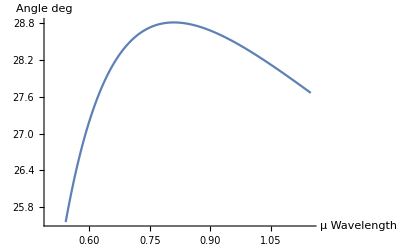

```mathematica
thetafinder[incre_]:=Module[{theta,λp,λs,λi,nop,nep,nos,nes,noi,nei},λp=0.405;λs=0.5+incre 0.0005;λi=(λs λp)/(λs-λp);nop=nord[λp];nep=next[λp];nos=nord[λs];nes=next[λs];noi=nord[λi];nei=next[λi];theta=ArcCos[√(((nep^2*nop^2)/((nos/λs+noi/λi)^2*λp^2)-nop^2)/(nep^2-nop^2))]*180/π;Return[theta];]
WAVELENGTHLIMIT=1300;
Clear[thetalist,index];
thetalist=Table[0,{i,WAVELENGTHLIMIT}];
For[index=1,index<WAVELENGTHLIMIT+1,thetalist⟦index⟧=thetafinder[index];index++;];
DataTable=Table[{0.5+i 0.0005,thetalist⟦i⟧},{i,WAVELENGTHLIMIT}];
ListPlot[DataTable,AxesLabel->{Wavelength μ,Angle deg},Joined->True]
```

-Graphics-
We want to calculate the thickness of the precompensation (L_pc) and compensation (L_c) YVO4 crystals. We start by drawing out the layout the crystal orientations. In SPEQS-I the downconversion BBO has thickness L = 6mm. The crystal axis of each crystal is labelled. Essentially we want to find out the difference between the H and V photons for each colour (signal and idler). 
As can be seen from the diagram, BBO 3 and 4 has symmertric delay for H and V polarizations and therefore can be omitted in the calcuations. Furthermore, the order of BBO 3 and 4 does not matter (but the crystal axis orientation matters for the spatial walkoff). 
BBO 1 and 2 there is some form of symmetry in the delay time. Essentially, only the circled time delay is being included for HH and VV path, as the rest is symmetric.
Narrow bandwidth of pump means long coherence length/time. If a narrow bandwidth pump is used, then no difference in temporal retardation in BBO1 (o_p -> 0 in diagram), thus pre-compensation is not needed. 
SPDC is a broadband process, hence the photon pairs created in BBO1 is broadband and thus the difference must be accounted for (e_s e_i in diagram) when the photon pairs pass through BBO2. If SPDC is a narrow band process then post-compensation is not needed.
We can have four equations for the time taken for signal and idler in the H and V polarizations:

T(H_s) = L_pc/(V_pc(p,o)) + L/(V_BBO(p,o))+ L_c/(V_c(s,e))
T(H_i) = L_pc/(V_pc(p,o)) + L/(V_BBO(p,o)) + L_c/(V_c(i,e))
T(V_s) = L_pc/(V_pc(p,e))+ L/(V_BBO(s,e)) + L_c/(V_c(s,o))
T(V_i) = L_pc/(V_pc(p,e))+ L/(V_BBO(i,e)) + L_c/(V_c(i,o))

we need to solve for L_pc and L_c using:

T(H_s) - T(V_s) = 0
T(H_i) - T(V_i) = 0

We define the group velocity of bbo and yvo4 in the next section:

```mathematica
ordindex[λ_]:=√(2.7359+0.01878/(λ λ-0.01822)-0.01354 λ λ);
extindex[λ_]:=√(2.3753+0.01224/(λ λ-0.01667)-0.01516 λ λ);
airindex[λ_]:=1.000287566+1.3412/((10^18 (λ λ))/10^12);
dnodl[λ_]:=(-0.02708 λ-(0.03756 λ)/((-0.01822+λ^2)^2))/(2 √(2.7359-0.01354 λ^2+0.01878/(-0.01822+λ^2)));
dnedl[λ_]:=(-0.03032 λ-(0.02448 λ)/((-0.01667+λ^2)^2))/(2 √(2.3753-0.01516 λ^2+0.01224/(-0.01667+λ^2)));
dneffdl[λ_,θ_]:=-1/2 (-((-0.02708 λ-(0.03756 λ)/((-0.01822+λ^2)^2)) Cos[θ]^2)/((2.7359-0.01354 λ^2+0.01878/(-0.01822+λ^2))^2)-((-0.03032 λ-(0.02448 λ)/((-0.01667+λ^2)^2)) Sin[θ]^2)/((2.3753-0.01516 λ^2+0.01224/(-0.01667+λ^2))^2)) (1/(Cos[θ]^2/(2.7359-0.01354 λ^2+0.01878/(-0.01822+λ^2))+Sin[θ]^2/(2.3753-0.01516 λ^2+0.01224/(-0.01667+λ^2))))^(3/2);
yvooindex[λ_]:=Sqrt[3.77834 + 0.069736/(λ^2-0.04724)- 0.0108133λ λ];
yvoeindex[λ_]:= Sqrt[4.59905 + 0.110534/(λ^2-0.04813)-0.0122676 λ λ];
dyvooindexdl[λ_]:=(-0.0216266 λ-(0.139472 λ)/((-0.04724+λ^2)^2))/(2 √(3.77834-0.0108133 λ^2+0.069736/(-0.04724+λ^2)));

dyvoeindexdl[λ_]:=(-0.024534 λ-(0.221068 λ)/((-0.04813+λ^2)^2))/(2 √(4.59905-0.012267 λ^2+0.110534/(-0.04813+λ^2)));
C1=300000000;
bboogroupvel[λ_,θpm_,δ_]:=Module[{u,no},
no=ordindex[λ];
u=1/(no - λ dnodl[λ]);
Return[C1 u];];
bboegroupvel[λ_,θpm_,δ_]:=Module[{u,no,ne,neff,θ},
no=ordindex[λ];ne=extindex[λ];
θ=θpm-δ;
neff=Sqrt[1/((Cos[θ]/no)^2 + (Sin[θ]/ne)^2)];
(*neff=Sqrt[1/(1/no^2 + (1/ne^2 - 1/no^2)(Sin[θ])^2)];*)
u=1/(neff - λ dneffdl[λ,θ]);
Return[C1 u];];
yvoogroupvel[λ_]:=Module[{u,no},
no=yvooindex[λ];
u=1/(no - λ dyvooindexdl[λ]);
Return[C1 u];];
yvoegroupvel[λ_]:=Module[{u,ne},
ne=yvoeindex[λ];
u=1/(ne - λ dyvoeindexdl[λ]);
Return[C1 u];];
neff[λ_,θ_]:=Module[{no,ne},
no=ordindex[λ];
ne=extindex[λ];
Return[Sqrt[1/(1/no^2 + (1/ne^2 - 1/no^2)(Sin[θ])^2)]];
];
```

We use the pump as 405nm, BBO cutting angle as 28.7591 degree, signal at 760nm.

```mathematica
P=0.405 
TP=28.7591*3.142/180 
S=0.76 
Id=((P*S)/(S-P))
```

0.405

0.502006

0.76

0.867042

Here we solve the two equations for Lpc and Lc:

T(H_i) - T(V_i) = 0 (1st equation)
T(H_s) - T(V_s) = 0 (2nd equation)

Here we using BBO1 & 2 L=6mm.

```mathematica
Solve[(Subscript[L, pc]/yvoogroupvel[P])+(0.006/bboogroupvel[P,TP,0])+(Subscript[L, c]/yvoegroupvel[Id])-((Subscript[L, pc]/yvoegroupvel[P])+(0.006/bboegroupvel[Id,TP,0])+(Subscript[L, c]/yvoogroupvel[Id]))==0&&(Subscript[L, pc]/yvoogroupvel[P])+(0.006/bboogroupvel[P,TP,0])+(Subscript[L, c]/yvoegroupvel[S])-((Subscript[L, pc]/yvoegroupvel[P])+(0.006/bboegroupvel[S,TP,0])+(Subscript[L, c]/yvoogroupvel[S]))==0,{Subscript[L, pc],Subscript[L, c]}]
```

{{L_pc→0.00344164,L_c→0.00311787}}

There is an alternative way to look at the compensation in the SPEQS unit in terms of phase. 
We first define wavenumber in material to be:

((k(γ))_α)^β=(2π n^β(λ_α,γ))/λ_α
where α = p (pump wavelength), s (signal wavelength) or i (idler wavelength)
β = e (extraordinary polarization) or o (ordinary polarization)
γ = bbo or yvo_4 (material)

When light (pump light, plane wave) with 45 degree polarization passes through an uniaxial crystal with length L, both the ordinary and extraordinary components pick up a (different) phase:

o+ e ⟶ Exp[ik_p^o L]o+Exp[ik_p^e L]e
= o + Exp[i(k_p^e-k_p^o)L]e
because since only the relative phase matters, it can be written in this way.

Now we can look at the SPEQS setup. 
At postion (I), the pump passes through the pre-compensator YVO_4 with length L_pc, therefore the wavefunction at (I) woud be:

ψ_I = Exp[((ik(yvo_4))_p)^o L_pc] o_p+ Exp[((ik(yvo_4))_p)^e L_pc] e_p
= o_p + Exp[i(((k(yvo_4))_p)^e-((k(yvo_4))_p)^o)L_pc] e_p
⧦ = o_p + Exp[iϕ_pc L_pc] e_p
where ϕ_pc = ((k(yvo_4))_p)^e-((k(yvo_4))_p)^o

At position (II) the pump has downconverted into signal and idler through type-I SPDC. The o-component of the pump (o_p) eventually becomes the H_s H_iand e-compoent of the pump (e_p) becomes the V_s V_i. Therefore the wavefunction at (II) will be:

ψ_I ⟶ ψ_II
ψ_I = o_p + Exp[iϕ_pc L_pc] e_p ⟶ ψ_II= Exp[((ik(bbo))_p)^o L] H_s H_i + Exp[iϕ_pc L_pc] {Exp[((ik(bbo))_s)^e L] V_s⊗ Exp[((ik(bbo))_i)^e L] V_i}
ψ_II = Exp[((ik(bbo))_p)^o L] H_s H_i + Exp[iϕ_pc L_pc] Exp[i(((ik(bbo))_s)^e+((ik(bbo))_i)^e)L] V_s V_i
= H_s H_i + Exp[iϕ_pc L_pc] Exp[i(((ik(bbo))_s)^e + ((ik(bbo))_i)^e - ((ik(bbo))_p)^o)L] V_s V_i
⧦ = H_s H_i + Exp[iϕ_pc L_pc] Exp[iϕ_dc L] V_s V_i
where ϕ_dc = ((k(bbo))_s)^e + ((k(bbo))_i)^e - ((k(bbo))_p)^o

At position (III) the downconverted photons experiences another phase shift based on their polairzation (V or H) because they experience a different refractive index (o or e) and also the phase shift depends on their wavelength. Therefore the transformation through post-compensation YVO_4 crystal with length L_c will be:

V_s ⟶ Exp[((ik(yvo_4))_s)^o L_c] V_s
V_i ⟶ Exp[((ik(yvo_4))_i)^o L_c] V_i
H_s ⟶ Exp[((ik(yvo_4))_s)^e L_c] H_s
H_i ⟶ Exp[((ik(yvo_4))_i)^e L_c] H_i

Therefore the wavefunction at (III) will be:

ψ_III = Exp[i(((k(yvo_4))_s)^e+((k(yvo_4))_i)^e)L_c] H_s H_i + Exp[iϕ_pc L_pc] Exp[iϕ_dc L] Exp[i(((k(yvo_4))_s)^o+((k(yvo_4))_i)^o)L_c]V_s V_i
= H_s H_i + Exp[iϕ_pc L_pc] Exp[iϕ_dc L] Exp[i(((k(yvo_4))_s)^o+((k(yvo_4))_i)^o-((k(yvo_4))_s)^e-((k(yvo_4))_i)^e)L_c]V_s V_i
⧦ = H_s H_i + Exp[i(ϕ_pc L_pc+ϕ_dc L+ϕ_c L_c)] V_s V_i
where ϕ_c = ((k(yvo_4))_s)^o+((k(yvo_4))_i)^o-((k(yvo_4))_s)^e-((k(yvo_4))_i)^e

The overall (relative) phase ϕ_pc L_pc+ϕ_dc L+ϕ_c L_c should be zero or close to zero after the compensations:

```mathematica
Subscript[ϕ, pc]=((2*Pi*yvoeindex[P]/P)-(2*Pi*yvooindex[P]/P))*0.00344164
```

0.0141318

```mathematica
Subscript[ϕ, dc]=((2*Pi*neff[S,TP]/S)+(2*Pi*neff[Id,TP]/Id)-(2*Pi*ordindex[P]/P))*0.006
```

-0.00565235

```mathematica
Subscript[ϕ, c]=((2*Pi*yvooindex[S]/S)+(2*Pi*yvooindex[Id]/Id)-(2*Pi*yvoeindex[S]/S)-(2*Pi*yvoeindex[Id]/Id))*0.00311787
```

-0.0103334

```mathematica
Subscript[ϕ, pc]+Subscript[ϕ, dc]+Subscript[ϕ, c]
```

-0.00185403

CHSH Inequality Calculations

-Graphics-

The CHSH Inequality states that:

-2 ≤ S ≤ 2

where

S = E(α_1, β_1) - E(α_1 , β_2) + E(α_2 , β_1) + E(α_2 , β_2)

The graph above shows a two-channel CHSH inequality setup. There are one waveplate in front of each PBS (a,b) which can be used to change the polarization of the photons (α,β). Typically the angles are choosen as the Bell’s angle to maximize the violation of the inequality.

α_1= 0°
α_2 = 45°
β_1 = 22.5°
β_2 = 67.5°

and E(α,β) = (N_(++)-N_(+-)-N_(-+)+N_(--))/(N_(++)+N_(+-)+N_(-+)+N_(--)) for each α and β angle settings. And N is the coincidence counts in each (D+, D-) detector. For example, N_(++) in E(α_1 , β_1) would means the coincidence counts between detector D+ abd D+ with α_1 set to 0° and β_2 set to 22.5°.

Now if only with 2 detectors (instead of 4 in the above setup), and we use 2xpolarizers or LCD+PBS setup, then each angle setting (i.e. α , β) need an extra setting at α + 90° and β + 90°. This because the detector at each side (A and B) will need to act as two detectors in the sense that the +90° setting will effectively switch from D+ to D-. By choosing α or α + 90° the detector can act as D+ or D- at will. Thus we have new definition for the angle choice:

α_1 = 0° (D+), 90° (D-)
α_2 = 45° (D+), 45°+90°=135° (D-)
β_1 = 22.5° (D+), 22.5°+90°=112.5° (D-)
β_2 = 67.5° (D+), 67.5°+90°=157.5°(D-)

Therefore we have:

For E(α_1 , β_1)
N_(++) → α_1 = 0°, β_1 = 22.5°
N_(--) → α_1 = 90°, β_1 = 112.5°
N_(+-) → α_1 = 0°, β_1 = 112.5°
N_(-+) → α_1 = 90°, β_1 = 22.5°

For E(α_1 , β_2)
N_(++) → α_1 = 0°, β_2 = 67.5°
N_(--) → α_1 = 90°, β_2 = 157.5°
N_(+-) → α_1 = 0°, β_2 = 157.5°
N_(-+) → α_1 = 90°, β_2 = 67.5°

For E(α_2 , β_1)
N_(++) → α_2 = 45°, β_1 = 22.5°
N_(--) → α_2 = 135°, β_1 = 112.5°
N_(+-) → α_2 = 45°, β_1 = 112.5°
N_(-+) → α_2 = 135°, β_1 = 22.5°

For E(α_2 , β_2)
N_(++) → α_2 = 45°, β_2 = 67.5°
N_(--) → α_2 = 135°, β_2 = 157.5°
N_(+-) → α_2 = 45°, β_2 = 157.5°
N_(-+) → α_2 = 135°, β_2 = 67.5°

Substitute these coincidence values into E(α,β) = (N_(++)-N_(+-)-N_(-+)+N_(--))/(N_(++)+N_(+-)+N_(-+)+N_(--)) and evaluate S = E(α_1, β_1) - E(α_1 , β_2) + E(α_2 , β_1) + E(α_2 , β_2)

Define CHSH measurement in different angle settings:

```mathematica
bellmeasurements={{{αp->0,βp->π/8,Npp->Npp1},{αp->0,βm->(5 π)/8,Npm->Npm1},{αm->π/2,βp->π/8,Nmp->Nmp1},{αm->π/2,βm->(5 π)/8,Nmm->Nmm1}},{{αp->0,βp->(3 π)/8,Npp->Npp2},{αp->0,βm->(7 π)/8,Npm->Npm2},{αm->π/2,βp->(3 π)/8,Nmp->Nmp2},{αm->π/2,βm->(7 π)/8,Nmm->Nmm2}},{{αp->π/4,βp->π/8,Npp->Npp3},{αp->π/4,βm->(5 π)/8,Npm->Npm3},{αm->(3 π)/4,βp->π/8,Nmp->Nmp3},{αm->(3 π)/4,βm->(5 π)/8,Nmm->Nmm3}},{{αp->π/4,βp->(3 π)/8,Npp->Npp4},{αp->π/4,βm->(7 π)/8,Npm->Npm4},{αm->(3 π)/4,βp->(3 π)/8,Nmp->Nmp4},{αm->(3 π)/4,βm->(7 π)/8,Nmm->Nmm4}}};
```

Define various E(α , β) functions here:

```mathematica
EValue[{Npp_,Npm_,Nmp_,Nmm_}]:= (Npp+Nmm -Nmp-Npm)/(Npp+Nmm+Nmp+Npm);
ΔEValue[{Npp_,Npm_,Nmp_,Nmm_}]:= Evaluate[Sqrt[(D[EValue[{Npp,Npm,Nmp,Nmm}],Npp]*Sqrt[Npp])^2 + (D[EValue[{Npp,Npm,Nmp,Nmm}],Nmm]*Sqrt[Nmm])^2 + (D[EValue[{Npp,Npm,Nmp,Nmm}],Npm]*Sqrt[Npm])^2 + (D[EValue[{Npp,Npm,Nmp,Nmm}],Nmp]*Sqrt[Nmp])^2]]
```

Define S = E(α_1, β_1) - E(α_1 , β_2) + E(α_2 , β_1) + E(α_2 , β_2) :

```mathematica
SValue[{Npp1_,Npm1_,Nmp1_,Nmm1_,Npp2_,Npm2_,Nmp2_,Nmm2_,Npp3_,Npm3_,Nmp3_,Nmm3_,Npp4_,Npm4_,Nmp4_,Nmm4_}]:=Evaluate[(EValue[{Npp,Npm,Nmp,Nmm}] /. Flatten[bellmeasurements[[1]]]) - (EValue[{Npp,Npm,Nmp,Nmm}] /. Flatten[bellmeasurements[[2]]]) +(EValue[{Npp,Npm,Nmp,Nmm}] /. Flatten[bellmeasurements[[3]]]) +(EValue[{Npp,Npm,Nmp,Nmm}] /. Flatten[bellmeasurements[[4]]])];
tmp={Npp1,Nmm1,Npm1,Nmp1,Npp2,Nmm2,Npm2,Nmp2,Npp3,Nmm3,Npm3,Nmp3,Npp4,Nmm4,Npm4,Nmp4};
```

Define the error in CHSH parameters using error propagations:

```mathematica
ΔSValue[{Npp1_,Npm1_,Nmp1_,Nmm1_,Npp2_,Npm2_,Nmp2_,Nmm2_,Npp3_,Npm3_,Nmp3_,Nmm3_,Npp4_,Npm4_,Nmp4_,Nmm4_}]:=
Evaluate[Sqrt[Total[Map[Function[x,D[SValue[{Npp1,Nmm1,Npm1,Nmp1,Npp2,Nmm2,Npm2,Nmp2,Npp3,Nmm3,Npm3,Nmp3,Npp4,Nmm4,Npm4,Nmp4}],x]^2*x],tmp] 
]
]
]
```

Testing:

```mathematica
μbell = αβ[α,β].dm[0].αβ[α,β] /. Flatten[bellmeasurements /.{αp->α,βp->β,αm->α,βm->β},1] //N
```

{0.426777,0.0732233,0.0732233,0.426777,0.0732233,0.426777,0.426777,0.0732233,0.426777,0.0732233,0.0732233,0.426777,0.426777,0.0732233,0.0732233,0.426777}

```mathematica
testcoinc=Map[Function[x,RandomVariate[PoissonDistribution[x]]] ,μbell*1500+120]
SValue[testcoinc] //N
ΔSValue[testcoinc] //N
```

{793,207,243,734,218,764,758,247,797,206,256,729,764,214,229,813}

2.17332

0.0447652

Input of the coincidences data from experiment:

α_1 =0°,β_1 =22.5°

```mathematica
Npp1=793;
```

α_1 =0°,β_1 =112.5°

```mathematica
Npm1=207;
```

α_1 =90°,β_1 =22.5°

```mathematica
Nmp1=243;
```

α_1 =90°,β_1 =112.5°

```mathematica
Nmm1=734;
```

α_1 =0°,β_2 =67.5°

```mathematica
Npp2=218;
```

α_1 =0°,β_2 =157.5°

```mathematica
Npm2=764;
```

α_1 =90°,β_2 =67.5°

```mathematica
Nmp2=758;
```

α_1 =90°,β_2 =157.5°

```mathematica
Nmm2=247;
```

α_2 =45°,β_1 =22.5°

```mathematica
Npp3=797;
```

α_2 =45°,β_1 =112.5°

```mathematica
Npm3=206;
```

α_2 =135°,β_1 =22.5°

```mathematica
Nmp3=256;
```

α_2 =135°,β_1 =112.5°

```mathematica
Nmm3=729;
```

α_2 =45°,β_2 =67.5°

```mathematica
Npp4=764;
```

α_2 =45°,β_2 =157.5°

```mathematica
Npm4=214;
```

α_2 =135°,β_2 =67.5°

```mathematica
Nmp4=229;
```

α_2 =135° β_2 =157.5°

```mathematica
Nmm4=813;
```

Evaluate CHSH S parameters using the above input:

```mathematica
N[SValue[{Npp1,Npm1,Nmp1,Nmm1,Npp2,Npm2,Nmp2,Nmm2,Npp3,Npm3,Nmp3,Nmm3,Npp4,Npm4,Nmp4,Nmm4}]]
```

2.17332

Evaluate the error in the S parameters:

```mathematica
N[ΔSValue[{Npp1,Npm1,Nmp1,Nmm1,Npp2,Npm2,Nmp2,Nmm2,Npp3,Npm3,Nmp3,Nmm3,Npp4,Npm4,Nmp4,Nmm4}]]
```

0.0447652